```mathematica
BATSET=Import["D:\\Documents\\works\\Datas\\Astrophysics\\Reference\\GRB\\BATSEtime.txt","Table"];
GRBNT90=BATSET[[All,5]];
GRBNT90Err=BATSET[[All,6]];
```

```mathematica
Bindx=Table[10^i,{i,-2.0,3.1,0.1}];
GRBct=BinCounts[GRBNT90,{Bindx}];
GRBNT=Table[{Log10[(Bindx[[i]]+Bindx[[i+1]])/2.0],GRBct[[i]]},{i,1,Length[GRBct],1}];
GRBNTb=Table[{Log10[Bindx[[i]]],GRBct[[i]]},{i,1,Length[GRBct],1}];
```

```mathematica
GRBNTf=NonlinearModelFit[GRBNT,a1*PDF[NormalDistribution[μ1,s1],x]+a2*PDF[NormalDistribution[μ2,s2],x],{a1,μ1,s1,a2,μ2,s2},x]
```

FittedModel[125.764 ⅇ^(-3.04608 ((«1»«1»)^2)+42.0851 ⅇ^(-«19» «1»)]

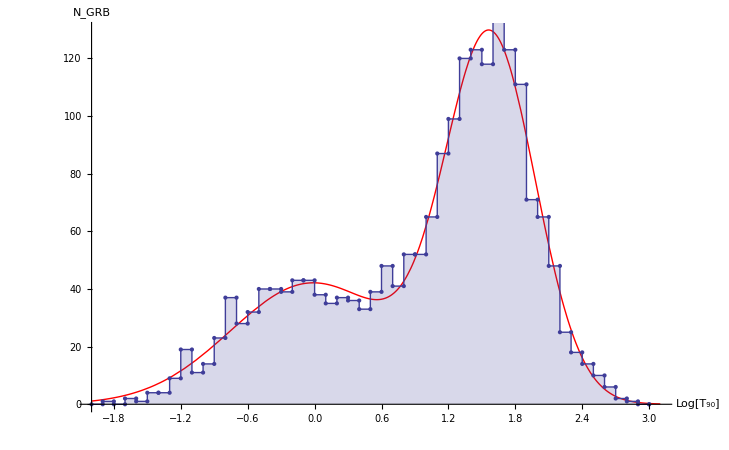

```mathematica
Show[Plot[GRBNTf[x],{x,-2,3.1},PlotStyle->Red],
ListPlot[GRBNTb,Joined->True,Filling->Axis,Mesh->All,InterpolationOrder->0],AxesOrigin->{-2,0},AxesLabel->{"Log[T_90]","N_GRB"}]
```

```mathematica
Export["D:\\Documents\\works\\Datas\\Astrophysics\\Reference\\GRB\\GRBNTf.csv",GRBNTf["ParameterTable"]]
```

D:\Documents\works\Datas\Astrophysics\Reference\GRB\GRBNTf.csv

```mathematica
GRBNTf["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 127.72 | 4.59734 | 27.7813 | 5.74629×10^-30
μ1 | 1.5766 | 0.0123358 | 127.807 | 2.81182×10^-59
s1 | 0.405148 | 0.0115851 | 34.9716 | 2.86707×10^-34
a2 | 77.5764 | 5.30983 | 14.61 | 1.07476×10^-18
μ2 | -0.0180514 | 0.0561173 | -0.321673 | 0.74919
s2 | 0.735378 | 0.0581133 | 12.6542 | 1.99897×10^-16

```mathematica
Means=GRBNTf["ParameterTable"][[1,1]][[All,2]];
Errors=GRBNTf["ParameterTable"][[1,1]][[All,3]];
```

```mathematica
PeakM1up=10^(Means[[3]]+Errors[[3]])
PeakM1down=10^(Means[[3]]-Errors[[3]])
PeakM1=10^Means[[3]]
PeakM2up=10^(Means[[6]]+Errors[[6]])
PeakM2down=10^(Means[[6]]-Errors[[6]])
PeakM1=10^Means[[6]]
Rp12=Means[[2]]/Means[[5]]
```

38.8091

36.6659

37.7223

1.09161

0.843007

0.959287

1.64638